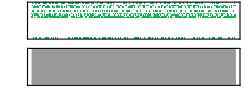

```mathematica
rule=ArrayRules[ToString/@{C,D,E,F5,G,A1,B3,C5,d5,C3}];
length=Sound[SoundNote@@@Table[{{RealDigits[N[Pi,#]][[1,i]]},.3,"Guitar"},{i,#}]/.rule]&;
length[1000]
```

```mathematica
SparseArray[{{1,1}->1,{2,2}->2}]
```

SparseArray[<2>, {2, 2}]

```mathematica
SparseArray[{{1,1}->1,{2,2}->2}]//ArrayRules
```

{{1,1}→1,{2,2}→2,{_,_}→0}

```mathematica
rule=ArrayRules[{10,110,50}]
```

{{1}→10,{2}→110,{3}→50,{_}→0}

```mathematica
{{1},{2,22,222},{4,5,6}}/.rule
```

{10,{2,22,222},{4,5,6}}

```mathematica
RealDigits[N[Pi*100,4]][[1,1]]
```

3

```mathematica
SoundNote@@@Table[{{RealDigits[N[Pi,3]][[1,i]]},.46,"Piano"},{i,3}]/.rule
```

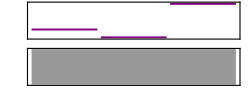

```mathematica
{SoundNote["E",0.46,"Piano"],SoundNote["C",0.46,"Piano"],SoundNote["F5",0.46,"Piano"]}//Sound
```

```mathematica
rule=ArrayRules[ToString/@{C,D,E,F5,G,A1,B3,C5,D5,C3}]
```

{{1}→C,{2}→D,{3}→E,{4}→F5,{5}→G,{6}→A1,{7}→B3,{8}→C5,{9}→D5,{10}→C3,{_}→0}

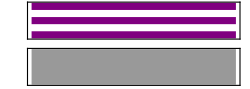

```mathematica
Sound@SoundNote[{0,2,4},1,"Piano"]
```

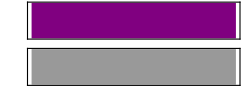

Sound`ToSampledSound::fontnf: The sound font file Standard1 cannot be installed.

```mathematica
Sound[SoundNote["BellTree"]]
```

```mathematica
Sound[SampledSoundList[Table[Sin[2π 500 t],{t,0,1,1./2000}],440]]
```

-Graphics-

```mathematica
Sound[SampledSoundList[Table[Sin[2π 500 t],{t,0,1,1./2000}],2000]]
```

-Graphics-

```mathematica
Sound[{Play[Sin[1000t(1+t^2)],{t,0,.2}],Play[Sin[500t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

```mathematica
{Play[Sin[440*2*Pi*t],{t,0,1}], Sound@SoundNote["A"]}
```

{-Graphics-,-Graphics-}